## Exact Solution: Bistable spring system

The problem was reduced to

(c_o^2-v^2)/2(du/dz)^2=ψ[u].

Integrating,

```mathematica
∫(ⅆ u)/(√((1-u)^2+d^2)-lo)
```

-ArcSinh[1-u]+1/(√2)(2 Log[2-u]-2 Log[u]+Log[2-u+√2 √(2-2 u+u^2)]-Log[u+√2 √(2-2 u+u^2)])

Converting the ArcTan terms to Log,

```mathematica
a[x_] := (-1+x)/(√(lo^2-d^2));
b[x_] := (lo (-1+x))/(√(lo^2-d^2) √(d^2+(-1+x)^2));
z[x_]:=√((co^2-v^2)/2)Log[(1-a[x])/(1+a[x])(1-b[x])/(1+b[x])(x-1+√((x-1)^2+d^2))^((2 √(lo^2-d^2))/lo)]
```

Parameters

```mathematica
lo=√2;
d=1;
co=√10;
v=2.835;
```

Inverse plot

Anti - Soliton Plot

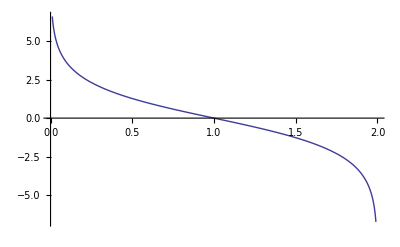

```mathematica
Plot[z[x],{x,0,2}]
```

Soliton Plot

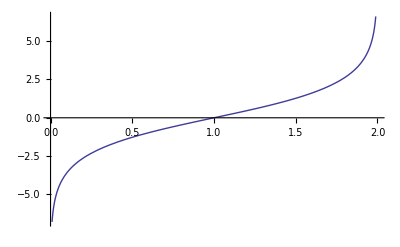

```mathematica
Plot[-z[x],{x,0,2}]
```

```mathematica
Series[z[x],{x,0,1}]
Series[z[x],{x,2,1}]
```

(1.00082-2.40296 Log[x])-0.60074 x+O[x]^2

(-1.00082+2.40296 Log[-2+x])-0.60074 (x-2)+O[x-2]^2

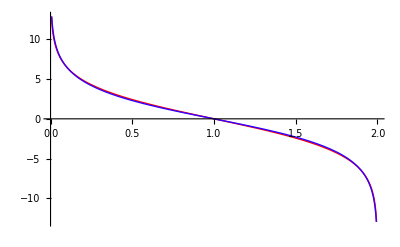

```mathematica
f[x_]:=2.2(-Log[x]+Log[2-x])
Plot[{f[x],z[x]},{x,0,2},PlotStyle->{Hue[0],Hue[0.7]}]
```

```mathematica
Solve[f[x]==u,x]
```

{{x→2./(1.+ⅇ^(0.454545 u))}}

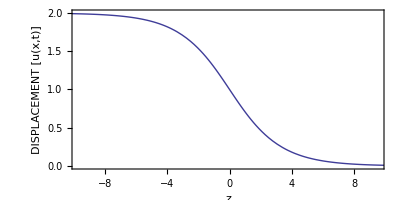

```mathematica
ParametricPlot[{z[x],x},{x,0,2}, Frame->True,AspectRatio->1/2, FrameLabel->{"z","DISPLACEMENT [u(x,t)]"}]
```

```mathematica
Energy[u_]:=(10 √2*0.53284)/(√(10-u^2))
```

```mathematica
Solve[Energy[u]==8,u]
```

{{u→-3.01873},{u→3.01873}}